# 化合物検索アルゴリズムの開発

## Program

```mathematica
home="/home/kamano/"
```

/home/kamano/

```mathematica
(*home="/Users/kouamano/"*)
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/List_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]
```

```mathematica
Get[home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Chemicalform_operations.txt"]
```

```mathematica
(*trReplace[mat_,li_]:=Module[{rls},
rls=Table[{n,n}->li[[n]],{n,Length[li]}];
ReplacePart[mat,rls]
]*)
```

```mathematica
(*elementAdjMat[mat_,vlist_]:=Module[{tr},
If[(Map[Head,vlist]//Flatten//Union)=={String},
tr=Map[ElementData[#,"AtomicNumber"]&,vlist],
tr=vlist
];
trReplace[mat,tr]
]*)
```

## 技術調査

## スペクトラルグラフ理論とは

グラフの隣接行列を特性方程式問題として扱う:

インプット = > 隣接行列
アウトプット = > 固有値・固有ベクトル
パラメーター => 
	- コネクション要素の値
	- トレースの値
	- ベースの値
	- 有向/無向

```mathematica
{{a,B,B,X},
{B,b,B,B},
{B,B,c,X},
{X,B,X,d}}//MatrixForm
```

(a | B | B | X
B | b | B | B
B | B | c | X
X | B | X | d)

B : ベース; X : コネクション(配置が対称なら無向); {a,b,c,d} : トレース。
Xの配置のみが決まっており、あとは編集可。



```mathematica
v={1,2,3,4};e={1<->2,1<->3,1<->4};g=Graph[v,e]
```

```mathematica
(am=AdjacencyMatrix[g])//MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
(es=Eigensystem[am]);{es[[1]]//MatrixForm,es[[2]]//MatrixForm}//TableForm
```

(-√3
√3
0
0)
(-√3 | 1 | 1 | 1
√3 | 1 | 1 | 1
0 | -1 | 0 | 1
0 | -1 | 1 | 0)

```mathematica
eval=es[[1]];evec=es[[2]];
```

## 隣接行列とその固有値・固有ベクトル(を求めるアルゴリズム)の一般的な性質

固有値はノルムの大きい順に求まる

固有値の合計は変化しない

固有ベクトルのノルムは1となる(Mathematicaではそうならない)

固有ベクトルの転置 (ベクトル) は直行する(対称行列)

```mathematica
Transpose[evec][[1]].Transpose[evec][[2]]
```

0

行・列を同じオーダーで入れ替えても固有値の求まる順は同じ、ただし固有ベクトルの要素の順は変更される

```mathematica
Eigenvalues[matReOrder[AdjacencyMatrix[g]//Normal,{3,2,4,1}]]
```

{-√3,√3,0,0}

## 隣接行列においてコネクションの強度がその固有値・固有ベクトルに及ぼす影響

```mathematica
ex1={{4,0,0,0},
{0,3,0,0},
{0,0,2,0},
{0,0,0,1}
}
```

{{4,0,0,0},{0,3,0,0},{0,0,2,0},{0,0,0,1}}

```mathematica
nex1=nEingensystem[ex1]
```

{{4,3,2,1},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}}

コネクションの強度が弱ければ、固有値列(パワースペクトル)への影響が少ない。

```mathematica
ex2={{4,0,0,0.1},
{0,3,0,0},
{0,0,2,0},
{0.1,0,0,1}
}
```

{{4,0,0,0.1},{0,3,0,0},{0,0,2,0},{0.1,0,0,1}}

```mathematica
nex2=nEingensystem[ex2]
```

{{4.00333,3.,2.,0.99667},{{-0.999446,0.,0.,-0.0332779},{0.,1.,0.,0.},{0.,0.,-1.,0.},{-0.0332779,0.,0.,0.999446}}}

```mathematica
Tr[nex2[[1]]]
```

10.

```mathematica
ex3={{4,0,0,1},
{0,3,0,0},
{0,0,2,0},
{1,0,0,1}
}
```

{{4,0,0,1},{0,3,0,0},{0,0,2,0},{1,0,0,1}}

```mathematica
nex3=nEingensystem[ex3]//N
```

{{4.30278,3.,2.,0.697224},{{0.957092,0.,0.,0.289784},{0.,1.,0.,0.},{0.,0.,1.,0.},{-0.289784,0.,0.,0.957092}}}

```mathematica
Tr[nex3[[1]]]
```

10.

```mathematica
ex4={{4,0,0,10},
{0,3,0,0},
{0,0,2,0},
{10,0,0,1}
}
```

{{4,0,0,10},{0,3,0,0},{0,0,2,0},{10,0,0,1}}

```mathematica
nex4=nEingensystem[ex4]//N
```

{{12.6119,-7.61187,3.,2.},{{0.75774,0.,0.,0.652556},{-0.652556,0.,0.,0.75774},{0.,1.,0.,0.},{0.,0.,1.,0.}}}

```mathematica
ex5={{4,0,0,-10},
{0,3,0,0},
{0,0,2,0},
{-10,0,0,1}
}
```

{{4,0,0,-10},{0,3,0,0},{0,0,2,0},{-10,0,0,1}}

```mathematica
nex5=nEingensystem[ex5]//N
```

{{12.6119,-7.61187,3.,2.},{{-0.75774,0.,0.,0.652556},{0.652556,0.,0.,0.75774},{0.,1.,0.,0.},{0.,0.,1.,0.}}}

```mathematica
Tr[nex5[[1]]]
```

10.

## スペクトラルグラフ理論を応用した化合物検索の先行事例

Milan Randic. 
On Characterization of Molecular Branching. 
Journal of The American Chemical Society. 
Vol.97, Num.23, p .6609. 
1975.

Frank R. Burden. 
Molecular Identification Number for Substructure Searches.
Journal of Chemical Information and Computer Sciences. 
Vol. 29, p.225. 
1989.

いずれも、系統の近い分子のマッチングに有効。

## アルゴリズム提案

本質的に、あらゆる系統の単独分子同士のマッチングに応用可能な方法を目指す。

## 技術コンセプト

固有値列 (パワースペクトル) のみを利用する

対角要素に原子番号を付与することにより原子集合を構成・区別する

固有ベクトルの差は無視する

パワースペクトルを大きく擾乱させない程度にコネクションの強度を設定することにより分子を区別できないか？

ひとまず2分子マッチを前提とする

双方の共通な原子集合を構成し、差異はコネクションを利用する

## アルゴリズム定義

### Pseudo Code

0   (***** Pseudo Code *****)
1   Compound A
2   Compound B
3
4   MC = MolCount (A, B)
5
6   BM[A] = AddBond (MC, A, tr = "Atomic number", bond = "Order", bg = 0)
7   BM[B] = AddBond (MC, B, tr = "Atomic number", bond = "Order", bg = 0)
8 
9    EVL[A] = Normalize (Eigenvalues (BM[A]))
10 EVL[B] = Normalize (Eigenvalues (BM[B]))
11
12  { IDX[A, B] = Inner (EVL[A], EVL[B])
13  OR
14  IDX[A, B] = Dist (EVL[A], EVL[B]) }
15  (* Parameters: tr,bond, bg. *)

### Work Flow

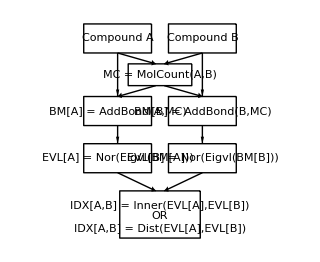

## 実装例

## Clustering of Amino Acid

```mathematica
cc=ChemicalData["Classes"];
```

```mathematica
AA=ChemicalData["AminoAcids"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
num = Length[AA]
```

20

```mathematica
AAName=Map[ChemicalData[#,"Name"]&,AA]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
AAFig=Map[ChemicalData[#]&,AA];
```

```mathematica
AAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, AAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(AAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,AA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},«18»,{«1»}}

```mathematica
AAVT=Map[ChemicalData[#,"VertexTypes"]&,AA]
```

{{C,C,N,O,O,H,H,H,H,H},{O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,N,O,O,H,H,H,H,C,O,C,H,H,H,H,H},{S,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,O,O,H,H,H,H,H,H,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{S,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,C,N,N,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,O,C,C,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,N,C,C,C,H,C,H,H,H,H,H,H,H,N,C,H,H,H,O,O,H}}

```mathematica
(elmAAAdjMat=Table[elementAdjMat[AAAdjMat[[n]],AAVT[[n]]],{n,Length[AAAdjMat]}])//Length
```

20

```mathematica
(AADmat=Outer[eigenSpectrumDistance,elmAAAdjMat,elmAAAdjMat,1])//Dimensions
```

{20,20}

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
ag["W"]=DirectAgglomerate[AADmat,Linkage->"Ward"]
```

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],4.67907,5,6],Cluster[Cluster[16,18,0.92273,1,1],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.592902,2,1],0.723301,1,3],3.19682,2,4],7.56004,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.97933,2,1],12.9788,17,3]

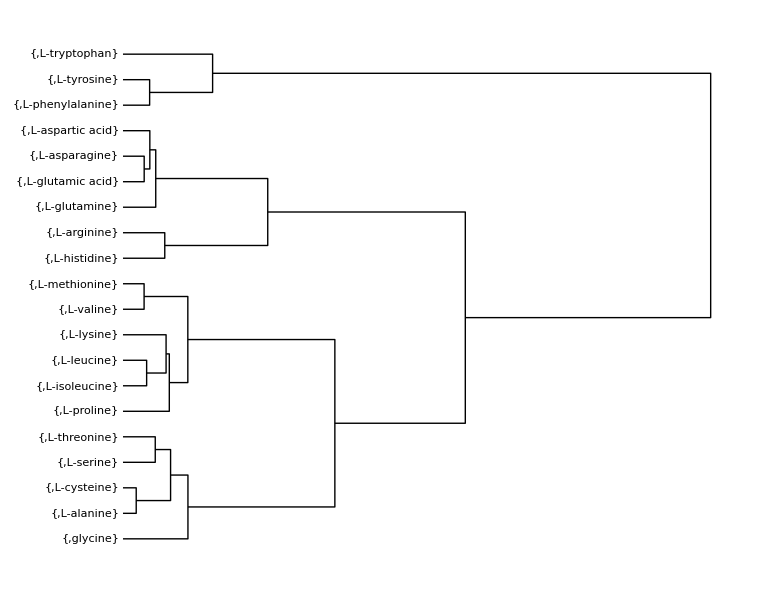

```mathematica
DendrogramPlot[ag["W"],LeafLabels->({AAFig45[[#]],AAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

## Clustering of Amino Acids + Lipids

Getting the information of lipids

```mathematica
LP=ChemicalData["Lipids"]
```

{heptane-1-13 C,heptane-d 16,octanoic acid-1-13 C,octanoic acid-1,2,3,4-13 C4,2-keto-4-methylpentanoic acid-1-13 csodium salt,octanoic-d 15 acid,sodium octanoate-1-13 C,menadione,decanoic acid-1-13 C,decanoic-d 19 acid,lauric acid-12-13 C,lauric acid-1-13 C,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-1-13 C,myristic acid-1,2-13 C2,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-1-13 C,palmitic acid-2-13 C,palmitic acid-1,2-13 C2,palmitic acid-2,2-d 2,palmitic acid-13 C16,oleic acid-1-13 C,stearic acid-1-13 C,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-1-13 C,potassium palmitate-2,2-d 2,oleic acid-13 C18,stearic-d 35 acid,octanoic acid-7-13 C,dodecylphosphorylcholine-d 38,α-tocopherol,glyceryl tri(octanoate-1-13 C),glyceryl-2-13 ctripalmitate,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
lipidsName=Map[ChemicalData[#,"Name"]&,LP]
```

{heptane-1-13 C,heptane-d 16,octanoic acid-1-13 C,octanoic acid-1,2,3,4-13 C4,2-keto-4-methylpentanoic acid-1-13 csodium salt,octanoic-d 15 acid,sodium octanoate-1-13 C,menadione,decanoic acid-1-13 C,decanoic-d 19 acid,lauric acid-12-13 C,lauric acid-1-13 C,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-1-13 C,myristic acid-1,2-13 C2,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-1-13 C,palmitic acid-2-13 C,palmitic acid-1,2-13 C2,palmitic acid-2,2-d 2,palmitic acid-13 C16,oleic acid-1-13 C,stearic acid-1-13 C,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-1-13 C,potassium palmitate-2,2-d 2,oleic acid-13 C18,stearic-d 35 acid,octanoic acid-7-13 C,dodecylphosphorylcholine-d 38,α-tocopherol,glyceryl tri(octanoate-1-13 C),glyceryl-2-13 ctripalmitate,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
isoQ=Table[StringMatchQ[lipidsName[[n]],RegularExpression[".*13 {0,1}[Cc].*"]],{n,Length[lipidsName]}]
```

{True,False,True,True,True,False,True,False,True,False,True,True,False,False,False,True,True,False,False,False,True,True,True,False,True,True,True,False,False,False,True,False,True,False,True,False,False,True,True,True,True}

```mathematica
nonIsoPos=Position[isoQ,False]
```

{{2},{6},{8},{10},{13},{14},{15},{18},{19},{20},{24},{28},{29},{30},{32},{34},{36},{37}}

```mathematica
lipidsNonIso=LP[[nonIsoPos//Flatten]]
```

{heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

Merging and Clustering

```mathematica
LPAA=Flatten[{AA,lipidsNonIso}]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
numLPAA=Length[LPAA]
```

38

```mathematica
LPAAName=Map[ChemicalData[#,"Name"]&,LPAA]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
(LPAAFig=Map[ChemicalData[#]&,LPAA])//Length
```

38

```mathematica
LPAAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, LPAAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(LPAAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,LPAA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},«36»,{«1»}}

```mathematica
LPAAVT=Map[ChemicalData[#,"VertexTypes"]&,LPAA]
```

{{C,C,N,O,O,H,H,H,H,H},{O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,N,O,O,H,H,H,H,C,O,C,H,H,H,H,H},{S,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,O,O,H,H,H,H,H,H,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{S,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,C,N,N,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,O,C,C,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,N,C,C,C,H,C,H,H,H,H,H,H,H,N,C,H,H,H,O,O,H},{C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{K,O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{P,O,O,O,O,N,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H}}

```mathematica
(elmLPAAAdjMat=Table[elementAdjMat[LPAAAdjMat[[n]],LPAAVT[[n]]],{n,Length[LPAAAdjMat]}])//Length
```

38

```mathematica
(LPAADmat=Outer[eigenSpectrumDistance,elmLPAAAdjMat,elmLPAAAdjMat,1])//Dimensions
```

{38,38}

```mathematica
lpaaag["W"]=DirectAgglomerate[LPAADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],Cluster[21,Cluster[22,24,1.00798,1,1],2.20387,1,2],3.62661,6,3],6.28158,5,9],Cluster[Cluster[16,18,0.92273,1,1],Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.592902,2,1],12,0.723301,3,1],3.19682,2,4],7.67005,14,6],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[34,31,0.,1,1],35,0.244229,2,1],Cluster[Cluster[30,28,0.,1,1],29,0.774995,2,1],2.23878,3,3],37,2.3346,6,1],Cluster[33,Cluster[32,36,0.,1,1],0.,1,2],3.68258,7,3],Cluster[27,Cluster[25,26,0.,1,1],0.,1,2],5.51745,10,3],Cluster[Cluster[Cluster[17,19,0.588454,1,1],Cluster[20,23,0.961533,1,1],2.31466,2,2],38,6.97161,4,1],10.7161,13,5],36.6737,20,18]

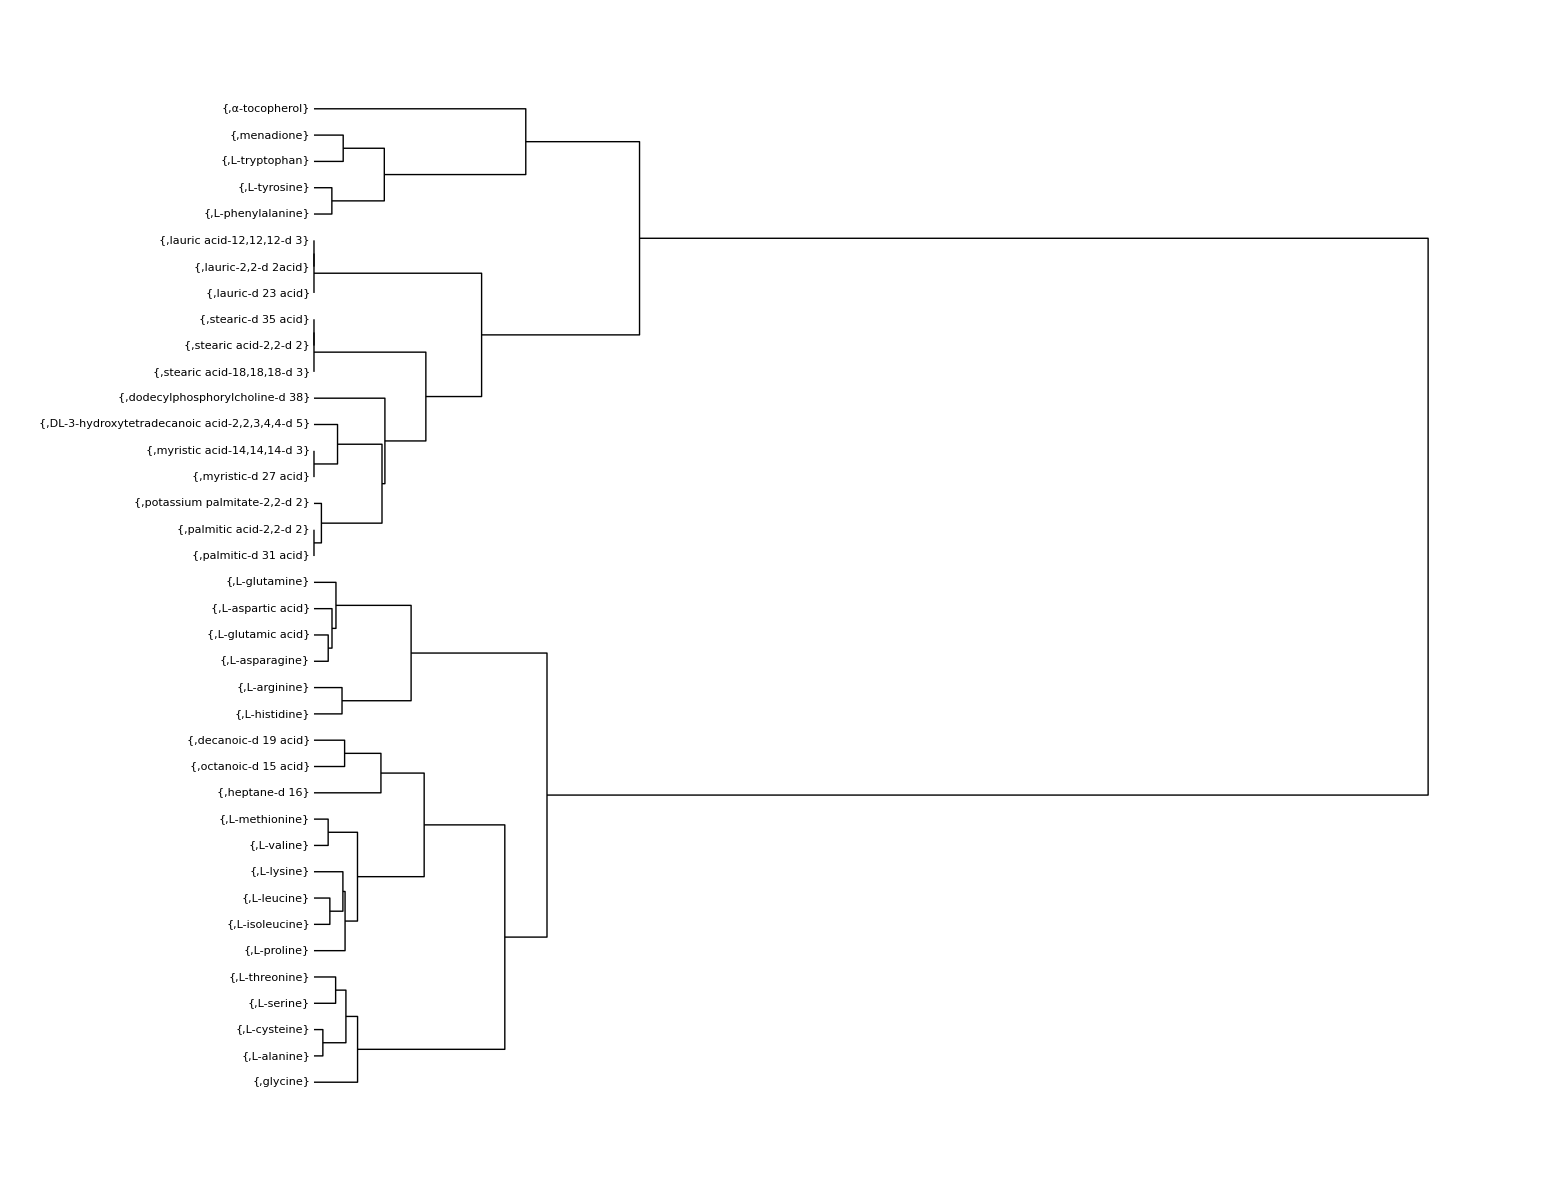

```mathematica
DendrogramPlot[lpaaag["W"],LeafLabels->({LPAAFig45[[#]],LPAAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```

## Chart

### Definitions

```mathematica
box[{x1_,y1_},{x2_,y2_}]:=Line[{{x1,y1},{x1,y2},{x2,y2},{x2,y1},{x1,y1}}]
```

### Object

```mathematica
coA={-1,0};coB={1,0}
```

{1,0}

Row1

```mathematica
bA=box[coA+{0,-0.75}+{0.8,0.2},coA+{0,-0.75}+{-0.8,-0.2}]
```

Line[{{-0.2,-0.55},{-0.2,-0.95},{-1.8,-0.95},{-1.8,-0.55},{-0.2,-0.55}}]

```mathematica
bB=box[coB+{0,-0.75}+{0.8,0.2},coB+{0,-0.75}+{-0.8,-0.2}]
```

Line[{{1.8,-0.55},{1.8,-0.95},{0.2,-0.95},{0.2,-0.55},{1.8,-0.55}}]

```mathematica
tA=Text["Compound A",coA+{0,-0.75}]
```

Text[Compound A,{-1,-0.75}]

```mathematica
tB=Text["Compound B",coB+{0,-0.75}]
```

Text[Compound B,{1,-0.75}]

Row2(not used)

```mathematica
bA2=box[coA+{0.8,0.2}+{0,-0.75},coA+{-0.8,-0.2}+{0,-0.75}]
```

Line[{{-0.2,-0.55},{-0.2,-0.95},{-1.8,-0.95},{-1.8,-0.55},{-0.2,-0.55}}]

```mathematica
bB2=box[coB+{0.8,0.2}+{0,-0.75},coB+{-0.8,-0.2}+{0,-0.75}]
```

Line[{{1.8,-0.55},{1.8,-0.95},{0.2,-0.95},{0.2,-0.55},{1.8,-0.55}}]

```mathematica
tA2=Text["CA[A] = CountAtoms(A)",coA+{0,-0.75}]
```

Text[CA[A] = CountAtoms(A),{-1,-0.75}]

```mathematica
tB2=Text["CA[B] = CountAtoms(B)",coB+{0,-0.75}]
```

Text[CA[B] = CountAtoms(B),{1,-0.75}]

Row3

```mathematica
bmc=box[{0,-1.25}+{0.75,0.15},{0,-1.25}+{-0.75,-0.15}]
```

Line[{{0.75,-1.1},{0.75,-1.4},{-0.75,-1.4},{-0.75,-1.1},{0.75,-1.1}}]

```mathematica
mc=Text["MC = MolCount(A,B)",{0,-1.25}]
```

Text[MC = MolCount(A,B),{0,-1.25}]

Row4

```mathematica
bA3=box[coA+{0.8,0.2}+{0,-1.75},coA+{-0.8,-0.2}+{0,-1.75}]
```

Line[{{-0.2,-1.55},{-0.2,-1.95},{-1.8,-1.95},{-1.8,-1.55},{-0.2,-1.55}}]

```mathematica
bB3=box[coB+{0.8,0.2}+{0,-1.75},coB+{-0.8,-0.2}+{0,-1.75}]
```

Line[{{1.8,-1.55},{1.8,-1.95},{0.2,-1.95},{0.2,-1.55},{1.8,-1.55}}]

```mathematica
tA3=Text["BM[A] = AddBond(A,MC)",coA+{0,-1.75}]
```

Text[BM[A] = AddBond(A,MC),{-1,-1.75}]

```mathematica
tB3=Text["BM[B] = AddBond(B,MC)",coB+{0,-1.75}]
```

Text[BM[B] = AddBond(B,MC),{1,-1.75}]

Row5

```mathematica
bA4=box[coA+{0.8,0.2}+{0,-2.4},coA+{-0.8,-0.2}+{0,-2.4}]
```

Line[{{-0.2,-2.2},{-0.2,-2.6},{-1.8,-2.6},{-1.8,-2.2},{-0.2,-2.2}}]

```mathematica
bB4=box[coB+{0.8,0.2}+{0,-2.4},coB+{-0.8,-0.2}+{0,-2.4}]
```

Line[{{1.8,-2.2},{1.8,-2.6},{0.2,-2.6},{0.2,-2.2},{1.8,-2.2}}]

```mathematica
tA4=Text["EVL[A] = Nor(Eigvl(BM[A]))",coA+{0,-2.4}]
```

Text[EVL[A] = Nor(Eigvl(BM[A])),{-1,-2.4}]

```mathematica
tB4=Text["EVL[B] = Nor(Eigvl(BM[B]))",coB+{0,-2.4}]
```

Text[EVL[B] = Nor(Eigvl(BM[B])),{1,-2.4}]

Row6

```mathematica
bidx=box[{0,-3}+{0.95,0.15},{0,-3}+{-0.95,-0.5}]
```

Line[{{0.95,-2.85},{0.95,-3.5},{-0.95,-3.5},{-0.95,-2.85},{0.95,-2.85}}]

```mathematica
tidx=Text["IDX[A,B] = Inner(EVL[A],EVL[B])
OR
IDX[A,B] = Dist(EVL[A],EVL[B])",{0,-3.2}]
```

Text[IDX[A,B] = Inner(EVL[A],EVL[B])
OR
IDX[A,B] = Dist(EVL[A],EVL[B]),{0,-3.2}]

Arrow

```mathematica
ar={Arrow[{coA+{0,-0.95},coA+{0,-1.55}}],Arrow[{coB+{0,-0.95},coB+{0,-1.55}}],
Arrow[{coA+{0,-0.95},coA+{0.9,-1.1}}],Arrow[{coB+{0,-0.95},coB+{-0.9,-1.1}}],
Arrow[{coA+{0.9,-1.4},coA+{0,-1.55}}],Arrow[{coB+{-0.9,-1.4},coB+{0,-1.55}}],
Arrow[{coA+{0,-1.95},coA+{0,-2.2}}],Arrow[{coB+{0,-1.95},coB+{0,-2.2}}],
Arrow[{coA+{0,-2.6},coA+{0.9,-2.85}}],Arrow[{coB+{0,-2.6},coB+{-0.9,-2.85}}]
}
```

{Arrow[{{-1,-0.95},{-1,-1.55}}],Arrow[{{1,-0.95},{1,-1.55}}],Arrow[{{-1,-0.95},{-0.1,-1.1}}],Arrow[{{1,-0.95},{0.1,-1.1}}],Arrow[{{-0.1,-1.4},{-1,-1.55}}],Arrow[{{0.1,-1.4},{1,-1.55}}],Arrow[{{-1,-1.95},{-1,-2.2}}],Arrow[{{1,-1.95},{1,-2.2}}],Arrow[{{-1,-2.6},{-0.1,-2.85}}],Arrow[{{1,-2.6},{0.1,-2.85}}]}

```mathematica
Graphics[{tA,bA,tB,bB(*,tA2,bA2,tB2,bB2*),mc,bmc,bA3,bB3,tA3,tB3,bA4,bB4,tA4,tB4,bidx,tidx,ar}]
```

-Graphics-